# The BES integral equation and the cusp anomalous dimension

## Preliminaries

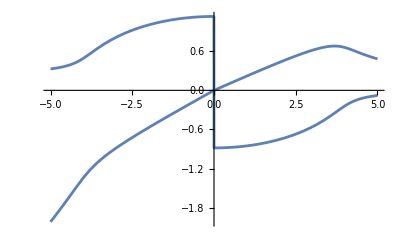
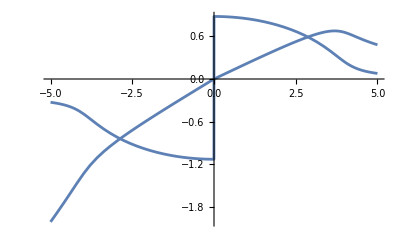

```mathematica
(*** express x^+ and x^- as functions of the spectral parameter u ***)
usub=Solve[{xp+1/xp==(u+I/2)/h,xm+1/xm==(u-I/2)/h},{xp,xm}][[1]];
xptrial[h_,u_]=xp/.usub;
xmtrial[h_,u_]=xm/.usub;

(*** wrong branch ***)
{Plot[{Re[xptrial[h,u]],Im[xptrial[h,u]]}/.{h->2.},{u,-5,5}],Plot[{Re[xmtrial[h,u]],Im[xmtrial[h,u]]}/.{h->2.},{u,-5,5}]}
```

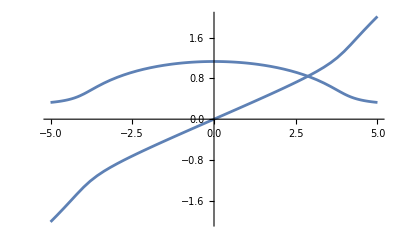
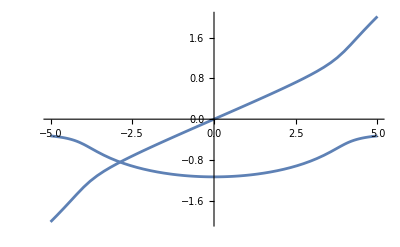

```mathematica
(*** fixing the branch choice ***)
xp[h_,u_]:=xptrial[h,u]/;u<0
xp[h_,u_]:=1/xptrial[h,u]/;u>=0
xm[h_,u_]:=xmtrial[h,u]/;u<0
xm[h_,u_]:=1/xmtrial[h,u]/;u>=0
{Plot[{Re[xp[h,u]],Im[xp[h,u]]}/.{h->2.},{u,-5,5}],
Plot[{Re[xm[h,u]],Im[xm[h,u]]}/.{h->2.},{u,-5,5}]}
```

```mathematica
(*** checking (23.130) ***)
LHSp[h_,m_,t_]:=NIntegrate[ ⅇ^(-ⅈ t u) (xp[h,u])^-m/(2Pi),{u,-Infinity,Infinity}]
RHSp[h_,m_,t_]:=(-I)^m m E^(-Abs[t]/2) BesselJ[m,2h t]/t
Ratiop[h_,m_,t_]:=LHSp[h,m,t]/RHSp[h,m,t]
{Ratiop[2.,1,.5],Ratiop[2.,1,-.5]}//Chop

LHSm[h_,m_,t_]:=NIntegrate[ ⅇ^(-ⅈ t u) (xm[h,u])^-m/(2Pi),{u,-Infinity,Infinity}]
RHSm[h_,m_,t_]:=-(-I)^m m E^(-Abs[t]/2) BesselJ[m,2h t]/t
Ratiom[h_,m_,t_]:=LHSm[h,m,t]/RHSm[h,m,t]
{Ratiom[2.,1,.5],Ratiom[2.,1,-.5]}//Chop
```

{1.,1.36093×10^-6}

{1.36093×10^-6,1.}

## Basic identities involving Bessel functions

```mathematica
(*** The "main kernel" Km is the first term on the RHS of (23.132) ***)
(*** Km == KmSum ***)
Km[t_,t1_] := (BesselJ[1,t] BesselJ[0,t1]-BesselJ[0,t] BesselJ[1,t1])/(t-t1);
KmSum[t_,t1_,cutoff_]:= 2/(t t1) Sum[n BesselJ[n,t] BesselJ[n,t1], {n,1,cutoff}];
{Km[2.,1.],KmSum[2.,1.,10]}

(*** Splitting Km=K0+K1 ***)
(*** K0 == K0Sum ***)
K0[t_,t1_] := (t BesselJ[1,t] BesselJ[0,t1]-t1 BesselJ[0,t] BesselJ[1,t1])/(t^2-t1^2);
K0Sum[t_,t1_,cutoff_] := 2/(t t1) Sum[(2n-1) BesselJ[2n-1,t] BesselJ[2n-1,t1], {n,1,cutoff}];
{K0[2.,1.],K0Sum[2.,1.,10]}

(*** K1 == K1Sum ***)
K1[t_,t1_] := (t1 BesselJ[1,t] BesselJ[0,t1]-t BesselJ[0,t] BesselJ[1,t1])/(t^2-t1^2);
K1Sum[t_,t1_,cutoff_] := 2/(t t1) Sum[(2n) BesselJ[2n,t] BesselJ[2n,t1], {n,1,cutoff}];
{K1[2.,1.],K1Sum[2.,1.,10]}
```

{0.342785,0.342785}

{0.261365,0.261365}

{0.0814207,0.0814207}

## The magic kernel

```mathematica
(*** coefficient Subscript[c, r,s](h) in the strong coupling expansion (23.107) ***)
cStrong[r_,s_,n_]:=Zeta[n]/((-2Pi)^n Gamma[n-1]) * (r-1)(s-1) Gamma[(s+r+n-3)/2]Gamma[(s-r+n-1)/2]/(Gamma[(s+r-n+1)/2] Gamma[(s-r-n+3)/2])/;n>=2
cStrong[r_,s_,1]:=-2/Pi (r-1)(s-1)/((s+r-2)(s-r))
cStrong[r_,s_,0]:=KroneckerDelta[s,r+1]

crsStrong[r_,s_,h_,horder_]:=Sum[cStrong[r,s,n] h^(1-n),{n,0,horder}]/;s>r
crsStrong[r_,s_,h_,horder_]:=Sum[-cStrong[s,r,n] h^(1-n),{n,0,horder}]/;s<r

(*** Splitting the kernel in (23.132) as K=Km+2Kc, following the convention of hep-th/0611135 ***)
KcOriginal[h_,t_,t1_,hord_,nn_]:=Module[{k,l},2/(t t1) Sum[(-1)^(k+l) crsStrong[2k,2l+1,h,hord] BesselJ[2l,t] BesselJ[2k-1,t1],{k,1,nn},{l,1,nn}]]

(*** the magic kernel ***)
Kc[h_,t_,t1_] := 4h^2 NIntegrate[K1[t,2h t2] t2/(E^t2-1) * K0[2h t2,t1], {t2,0,Infinity}];

(*** decomposition of magic kernel ***)
Z[h_, n_,m_] := NIntegrate[BesselJ[m,2h t] BesselJ[n, 2h t]/(t(E^t-1)), {t,0,Infinity}];
KcSum[h_,t_,t1_,cutoff_] := Sum[8n(2m-1)/(t t1) Z[h, 2n,2m-1] BesselJ[2n,t] BesselJ[2m-1,t1], {n,1,cutoff}, {m,1,cutoff}];
(*** checking that they are all the same ***)
{KcOriginal[2.,2.,.5,10,10],Kc[2.,2.,.5],KcSum[2.,2.,.5,5]}
```

{0.280495,0.280495,0.280495}

## Simplifying BES equation (pseudo code)

The BES equation (23.131) is equivalently written as
s[t] == K[2h t, 0] - 4h^2 Integrate[K[2h t,2h t1] * t1/(E^t1-1) * s[t1], {t1,0,Infinity}],

where 
s[t] = -(E^t-1)/t * σ[t].

We expand 
s[t] = Sum[ss[n] BesselJ[n,2h t]/(2h t),{n,1,Infinity}], 

and write BES equation as

s[t] == Km[2h t, 0] + 2 Kc[2h t, 0] - 4h^2 Integrate[Km[2h t,2h t1] * t1/(E^t1-1) * s[t1], {t1,0,Infinity}] - 8 h^2 Integrate[Kc[2h t,2h t1] * t1/(E^t1-1) * s[t1], {t1,0,Infinity}].

Following the notation of hep-th/0611135, here we split 
K[t,t1] = Km[t1,t1] + 2Kc[t,t1].

Using the identities checked above,

Km[t,t1] = 2/(t t1) Sum[n BesselJ[n,t] BesselJ[n,t1], {n,1,Infinity}],
K0[t,t1] = 2/(t t1) Sum[(2n-1) BesselJ[2n-1,t] BesselJ[2n-1,t1], {n,1,Infinity}],
K1[t,t1] = 2/(t t1) Sum[(2n) BesselJ[2n,t] BesselJ[2n,t1], {n,1,Infinity}],

and most nontrivially the magic kernel expression

Kc[t,t1] = Sum[8n(2m-1)/(t t1) Z[h, 2n,2m-1] BesselJ[2n,t] BesselJ[2m-1,t1], {n,1,Infinity}, {m,1,Infinity}],

where 
Z[h, n,m] = Integrate[BesselJ[m,2h t] BesselJ[n, 2h t]/(t(E^t-1)), {t,0,Infinity}],

we can rewrite BES equation as

Sum[ss[n] BesselJ[n,2h t]/(2h t),{n,1,Infinity}]
== 2/(2h t) Sum[n BesselJ[n,2h t] (D[BesselJ[n,t1],t1]/.t1->0), {n,1,Infinity}]
  + 2 Sum[8n(2m-1)/(2h t) Z[h, 2n,2m-1] BesselJ[2n,2h t] (D[BesselJ[2m-1,t1],t1]/.t1->0), {n,1,Infinity}, {m,1,Infinity}]
  - 4h^2 Sum[ss[n] * Integrate[Km[2h t,2h t1] * t1/(E^t1-1) * BesselJ[n,2h t1]/(2h t1), {t1,0,Infinity}], {n,1,Infinity}]
  - 8h^2 Sum[ss[n] * Integrate[Kc[2h t,2h t1] * t1/(E^t1-1) * BesselJ[n,2h t1]/(2h t1), {t1,0,Infinity}], {n,1,Infinity}],

and one step further,

Sum[ss[n] BesselJ[n,2h t]/(2h t),{n,1,Infinity}]
== 2/(2h t) Sum[n BesselJ[n,2h t] (D[BesselJ[n,t1],t1]/.t1->0), {n,1,Infinity}]
  + 2 Sum[8n(2m-1)/(2h t) Z[h, 2n,2m-1] BesselJ[2n,2h t] (D[BesselJ[2m-1,t1],t1]/.t1->0), {n,1,Infinity}, {m,1,Infinity}]
  - 4h^2 Sum[ss[n] * Integrate[2/(2h t 2h t1) Sum[m BesselJ[m,2h t] BesselJ[m,2h t1], {m,1,Infinity}] * t1/(E^t1-1) * BesselJ[n,2h t1]/(2h t1), {t1,0,Infinity}], {n,1,Infinity}]
  - 8h^2 Sum[ss[n] * Integrate[Sum[8k(2m-1)/(2h t 2h t1) Z[h, 2k,2m-1] BesselJ[2k,2h t] BesselJ[2m-1,2h t1], {k,1,Infinity}, {m,1,Infinity}] * t1/(E^t1-1) * BesselJ[n,2h t1]/(2h t1), {t1,0,Infinity}], {n,1,Infinity}].

Stripping off BesselJ[n,2h t]/(2h t) from both sides, we get

ss[n]
== 2 n (D[BesselJ[n,t1],t1]/.t1->0)
  + 2 KroneckerDelta[2k,n] Sum[8k(2m-1) Z[h, 2k,2m-1] (D[BesselJ[2m-1,t1],t1]/.t1->0), {m,1,Infinity}]
  - 4h^2 Sum[ss[k] * Integrate[2/(2h t1) n BesselJ[n,2h t1] * t1/(E^t1-1) * BesselJ[k,2h t1]/(2h t1), {t1,0,Infinity}], {k,1,Infinity}]
  - 8h^2 Sum[ss[l] * Integrate[Sum[8k(2m-1)/(2h t1) KroneckerDelta[2k,n] Z[h, 2k,2m-1] BesselJ[2m-1,2h t1], {m,1,Infinity}] * t1/(E^t1-1) * BesselJ[l,2h t1]/(2h t1), {t1,0,Infinity}], {l,1,Infinity}].
  
This is now of the form
ss[n] == hh[n] + Sum[KK[n,m] ss[m], {m,1,Infinity}],

where
hh[n] = 2 n (D[BesselJ[n,t1],t1]/.t1->0)
  + 2 KroneckerDelta[2k,n] Sum[8k(2m-1) Z[h, 2k,2m-1] (D[BesselJ[2m-1,t1],t1]/.t1->0), {m,1,Infinity}],

and
KK[n,m] = - 4h^2 Integrate[2/(2h t1) n BesselJ[n,2h t1] * t1/(E^t1-1) * BesselJ[m,2h t1]/(2h t1), {t1,0,Infinity}]
  - 8h^2 Integrate[Sum[8k(2p-1)/(2h t1) KroneckerDelta[2k,n] Z[h, 2k,2p-1] BesselJ[2p-1,2h t1], {p,1,Infinity}] * t1/(E^t1-1) * BesselJ[m,2h t1]/(2h t1), {t1,0,Infinity}]

## Now the numerical implementation

```mathematica
hh[h_,n_]:= 2 n (1/2 KroneckerDelta[n,1])+ 2 If[EvenQ[n],1,0] 4n Z[h, n,1] (1/2)

KK[h_,n_,m_,cutoff_]:= - 4h^2 NIntegrate[2/(2h t1) n BesselJ[n,2h t1] * t1/(E^t1-1) * BesselJ[m,2h t1]/(2h t1), {t1,0,Infinity}]- 8h^2 NIntegrate[Sum[4n(2p-1)/(2h t1) If[EvenQ[n],1,0] Z[h, n,2p-1] BesselJ[2p-1,2h t1], {p,1,cutoff}] * t1/(E^t1-1) * BesselJ[m,2h t1]/(2h t1), {t1,0,Infinity}]

hvector[h_,size_]:=Table[hh[h,n],{n,1,size}]
Kmatrix[h_,size_]:=Table[KK[h,n,m,size],{n,1,size},{m,1,size}]

svector[size_]:=Table[svar[n],{n,1,size}];
ssol[h_,size_]:=ssol[h,size]=Solve[svector[size]==hvector[h,size]+Transpose[Kmatrix[h,size].Transpose[{svector[size]}]][[1]],svector[size]][[1]]

strial[h_,t_,size_]:=Sum[svar[n] BesselJ[n,2h t]/(2h t),{n,1,size}]/.ssol[h,size];
Γcusp[h_,size_]:=4h^2(1+4h NIntegrate[-t/(E^t-1) strial[h,t,size] BesselJ[1,2h t]/t,{t,0,Infinity}])
```

## Testing that the solution indeed solves BES integral equation

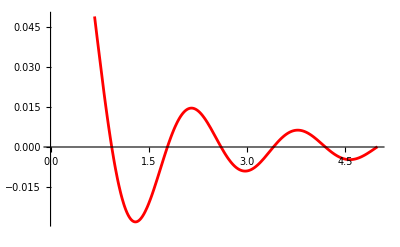
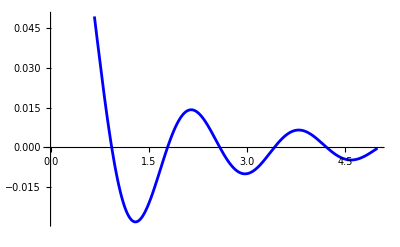

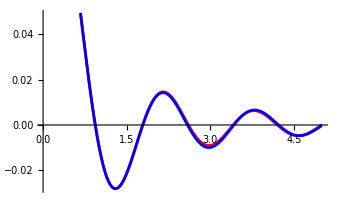

```mathematica
Kz[h_,t_,hord_,nn_]:=Module[{l},BesselJ[1,t]/t+2/t Sum[(-1)^(l-1) crsStrong[2,2l+1,h,hord] BesselJ[2l,t],{l,1,nn}]]
KOriginal[h_,t_,t1_,hord_,nn_]:=Module[{k,l},(BesselJ[1,t] BesselJ[0,t1]-BesselJ[0,t] BesselJ[1,t1])/(t-t1)+4/(t t1) Sum[(-1)^(k+l) crsStrong[2k,2l+1,h,hord] BesselJ[2l,t] BesselJ[2k-1,t1],{k,1,nn},{l,1,nn}]]

NN=5;horder=5;
htest=2.;testsize=8;
KOriginal[t_,t1_]=KOriginal[htest,t,t1,horder,NN];
Kz[t_]=Kz[htest,t,horder,NN];
stest[t_]=strial[htest,t,testsize];

BESOriginal[t_]:=Kz[2htest t] - 4htest^2 NIntegrate[KOriginal[2htest t,2htest t1] * t1/(E^t1-1) * stest[t1], {t1,0,Infinity}]

{a=Plot[stest[t],{t,0,5},PlotStyle->Red],
b=Plot[BESOriginal[t],{t,0,5},PlotStyle->Blue]}
Show[a,b]
```

## The numerical value of the cusp anomalous dimension

```mathematica
(*** comparison with (23.136), also accounting for the next order (for higher orders in the strong coupling expansion see arXiv:0708.3933) ***)
Γtarget[h_]:=2h-3Log[2]/(2Pi)-Catalan/(8Pi^2 h)
```

```mathematica
(*** h=1, size=8 and 10 ***)
{Γcusp[1.,8],Γcusp[1.,10]}
Γtarget[1.]
```

{1.65332,1.65332}

1.65745

```mathematica
(*** h=2, size=8 and 10 ***)
{Γcusp[2.,8],Γcusp[2.,10]}
Γtarget[2.]
```

{3.66229,3.66229}

3.66325

```mathematica
(*** h=10, size=8 and 10 ***)
{Γcusp[10.,8],Γcusp[10.,10],Γcusp[10.,12]}
Γtarget[10.]
```

{19.684,19.6657,19.6678}

19.6679